```mathematica
p1 = ParametricPlot[{ Sin[x],Cos[x]},{x,0,2π},PlotStyle->{Dashed,Black},Axes->False,GridLines->Automatic,Frame->True,FrameLabel->{"Pz","Px"},FrameStyle->Thick];
```

Powheg:

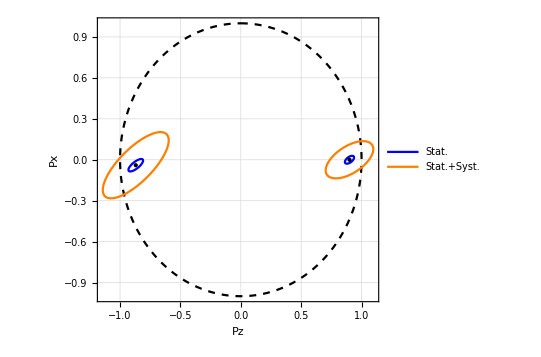

```mathematica
Powheg:

toptheo=Graphics[{PointSize[Medium],Black,Point[{0.90,0.00}]}];
antitoptheo=Graphics[{PointSize[Medium],Black,Point[{-0.87,-0.04}]}];

Powheg+Backgrounds (full systs):;
Corr ={{1,0.572},{0.572,1}} ;
StdDev = {{0.025,0},{0,0.019}};
S= StdDev.Corr.StdDev ;
InvS = Inverse[S];
f[x_,y_] := {{x,y}}.InvS.{{x},{y}};
p2=ContourPlot[Simplify[f[x-0.90,y-0.00]]==2.3,{x,-1+0.90,1+0.90},{y,-1+0.00,1+0.00},ContourStyle->Blue,Axes->True,AxesLabel->{Subscript[P, z],Subscript[P, x]},
PlotLegends->Placed[{"Stat."}, Above],PlotPoints->100];
StdDev = {{0.13,0},{0,0.09}};
S= StdDev.Corr.StdDev ;
InvS = Inverse[S];
f[x_,y_] := {{x,y}}.InvS.{{x},{y}};
p3=ContourPlot[Simplify[f[x-0.90,y-0.00]]==2.3,{x,-1+0.90,1+0.90},{y,-1+0.00,1+0.00},ContourStyle->Orange,PlotLegends->Placed[{"Stat.+Syst."}, Above],PlotPoints->100];

CorrAnti ={{1,0.751},{0.751,1}} ;
StdDevAnti = {{0.040,0},{0,0.030}};
SAnti= StdDevAnti.CorrAnti.StdDevAnti ;
InvSAnti = Inverse[SAnti];
fAnti[x_,y_] := {{x,y}}.InvSAnti.{{x},{y}};
p4=ContourPlot[Simplify[fAnti[x+0.87,y+0.04]]==2.3,{x,-1-0.87,1-0.87},{y,-1-0.04,1-0.04},ContourStyle->Blue,PlotPoints->100];
StdDevAnti = {{0.18,0},{0,0.16}};
SAnti= StdDevAnti.CorrAnti.StdDevAnti ;
InvSAnti = Inverse[SAnti];
fAnti[x_,y_] := {{x,y}}.InvSAnti.{{x},{y}};
p5=ContourPlot[Simplify[fAnti[x+0.87,y+0.04]]==2.3,{x,-2-0.87,1+0.87},{y,-1-0.04,1-0.04},ContourStyle->Orange,PlotPoints->100];

Show[{p1,p2,p3,p4,p5,toptheo,antitoptheo},PlotRange->All]
```

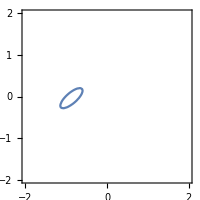

```mathematica
a=70.7896;b=-59.8085;c=89.5931;d=118.389;e=-96.8991;g=47.2613;
ellipse1=a x^2+2b x y+c y^2+d x+e y+g;
ContourPlot[ellipse1==0,{x,-2,2},{y,-2,2},ImageSize->200]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{u→-0.869999,v→-0.0400007,f2→-2.29984}

-2.29984+70.7896 x^2-119.617 x y+89.5931 y^2

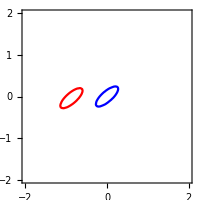

```mathematica
uv=First@Solve[ForAll[{x,y},a (x-u)^2+2 b (x-u) (y-v)+c (y-v)^2+f2==ellipse1],{u,v,f2},Reals]
ellipse2=ellipse1/.{x->x+u,y->y+v}/.uv//Simplify//Chop
ContourPlot[{ellipse1==0,ellipse2==0},{x,-2,2},{y,-2,2},ImageSize->200,ContourStyle->{Red,Blue},Axes->True,AxesOrigin->{0,0}]
```

{phi→0.707437}

-2.29984+19.6484 x^2+140.734 y^2

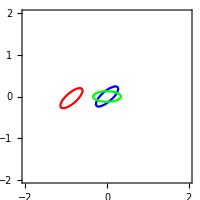

```mathematica
solphi=First@Solve[Tan[2 phi]==2 b/(a-c),phi]//Quiet
rotate=RotationMatrix[phi/.solphi].{x,y};
ellipse3=ellipse2/.{x->First@rotate,y->Last@rotate}//Simplify//Chop
ContourPlot[{ellipse1==0,ellipse2==0,ellipse3==0},{x,-2,2},{y,-2,2},ImageSize->200,ContourStyle->{Red,Blue,Green},Axes->True,AxesOrigin->{0,0}]
```

```mathematica
Sqrt[2.3/140.734]
```

0.127839

```mathematica
0.707437 /π * 180
```

40.5332

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{u→-0.869999,v→-0.0400007,f2→-2.29984}

-2.29984+70.7896 x^2-119.617 x y+89.5931 y^2

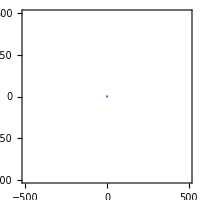

Protos:

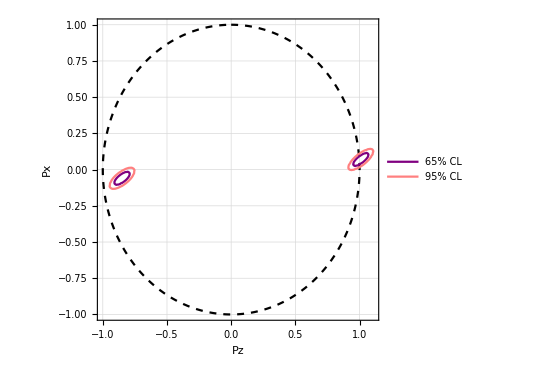

```mathematica
Protos:
Corr2 ={{1,0.754},{0.754,1}} ;
StdDev2 = {{0.04,0},{0,0.03}};
S2= StdDev2.Corr2.StdDev2 ;
InvS2 = Inverse[S2];
f2[x_,y_] := {{x,y}}.InvS2.{{x},{y}}
p22=ContourPlot[Simplify[f2[x-1.01,y-0.07]]==2.3,{x,-1+1.01,1+1.01},{y,-1+0.07,1+0.07},PlotRange->All,ContourStyle->Purple];
p32=ContourPlot[Simplify[f2[x-1.01,y-0.07]]==5.99,{x,-1+1.01,1+1.01},{y,-1+0.07,1+0.07},PlotRange->All,ContourStyle->Pink];

CorrAnti2 ={{1,0.696},{0.696,1}} ;
StdDevAnti2 = {{0.04,0},{0,0.03}};
SAnti2= StdDevAnti2.CorrAnti2.StdDevAnti2 ;
InvSAnti2 = Inverse[SAnti2];
fAnti2[x_,y_] := {{x,y}}.InvSAnti2.{{x},{y}}
p42=ContourPlot[Simplify[fAnti2[x+0.85,y+0.06]]==2.3,{x,-1-0.85,1-0.85},{y,-1-0.06,1-0.06},PlotRange->All,ContourStyle->Purple,PlotLegends->{"65% CL"}];
p52=ContourPlot[Simplify[fAnti2[x+0.85,y+0.06]]==5.99,{x,-1-0.85,1-0.85},{y,-1-0.06,1-0.06},PlotRange->All,ContourStyle->Pink,PlotLegends->{"95% CL"}];

Show[{p1,p22,p32,p42,p52},PlotRange->All]
```

```mathematica
point1={0.23,1.14};
point2={-0.18,-1};
pMarker1= ListPlot[{point1},PlotMarkers->{●,10},PlotLegends->{"BestFit_Top"}];
pMarker2= ListPlot[{point2},PlotMarkers->{■,15},PlotLegends->{"BestFit_AntiTop"},PlotStyle->Red];

shadinggraph=RegionPlot[550.3436636333992+172.48741623445065 x^2+x (579.4052631732134-608.6649700373177 y)-1155.3830223223495 y+606.4010726992407 y^2<=2.3 ,{x,-1,1},{y,-1+0.95,1+0.95},BoundaryStyle->None,PlotStyle->Lighter[Orange,.9],PlotRange->All];
```